```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)((17 + (Cos[theta])^2)/192/π)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-500, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
BOBmemScale2[scale1_, scale2_]:= Plot[MEMBOB[t, scale1, scale2]-MEMBOB[-500, scale1, scale2], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale2[a, b], {a, -0.9, 0.9}, {b, -0.9, 0.9}]
```

```mathematica
Eqn[α1_, α2_]:= NDSolve[{h'[t]==MEMBOB[t, α1, α2]-MEMBOB[-500, α1, α2], h[0]==0},h, {t, -60,40}]
```

```mathematica
Inthmem[scale_] := Plot[{Evaluate[h[t]/.Eqn[scale,scale]]}, {t,-40,40}, PlotRange->{{-40, 40},{-1.0,2.0}}]
```

```mathematica
Manipulate[Inthmem[n] , {n, -0.9, 0.9}]
```

```mathematica
Res[t_, α1_, α2_] :=h[t] /. Eqn[α1, α2]
```

```mathematica
generateBOBmemdata[α1_, α2_, ti_, tf_, dt_]:=Res[#, α1, α2]& /@ Range[ti, tf, dt]
```

```mathematica
dataBoBmem[α1_, α2_, ti_, tf_, dt_] :=Transpose@{Range[ti, tf, dt], generateBOBmemdata[ α1, α2, ti, tf, dt][[All, 1]]}
```

```mathematica
parabolaBoBmem[ t_, α1_, α2_, ti_, tf_, dt_]:=Fit[dataBoBmem[α1, α2, ti, tf, dt],{1,x,x^2},x]/.x-> t;
```

```mathematica
ResMquad[t_, α1_, α2_, ti_, tf_, dt_] := Res[t, α1, α2] - parabolaBoBmem[t, α1, α2, ti, tf, dt]
```

```mathematica
ResFinal[ α1_, α2_, ti_, tf_, dt_] :=Part[ResMquad[#, α1, α2, ti, tf, dt]& /@ Range[ti, tf, dt],  All, 1]
```

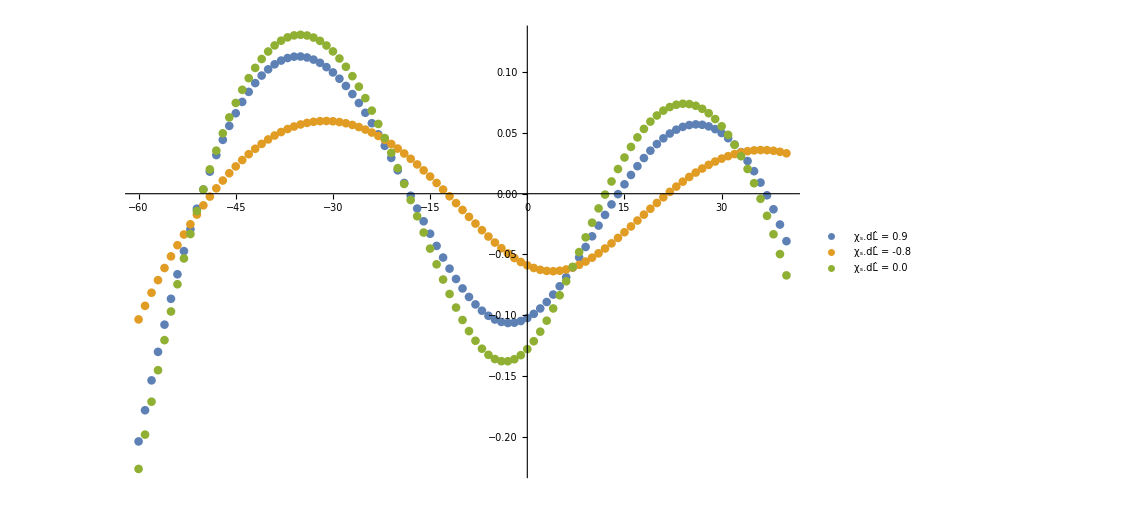

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60,40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,-0.8, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0,0, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = -0.8","χ_s.dL̂ = 0.0"},{0.120,0.87}]]
```

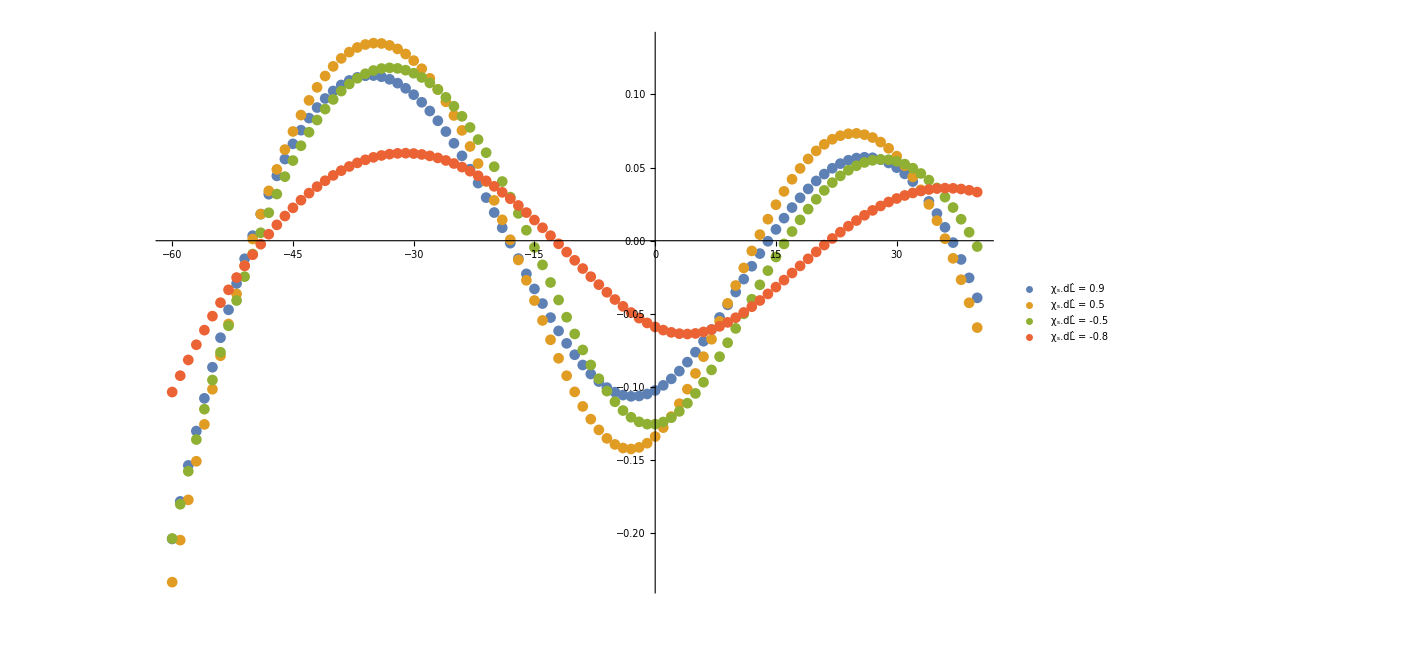

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60, 40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0.5,0.5, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.5,-0.5, -60, 40, 1 ]},Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,-0.8, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```

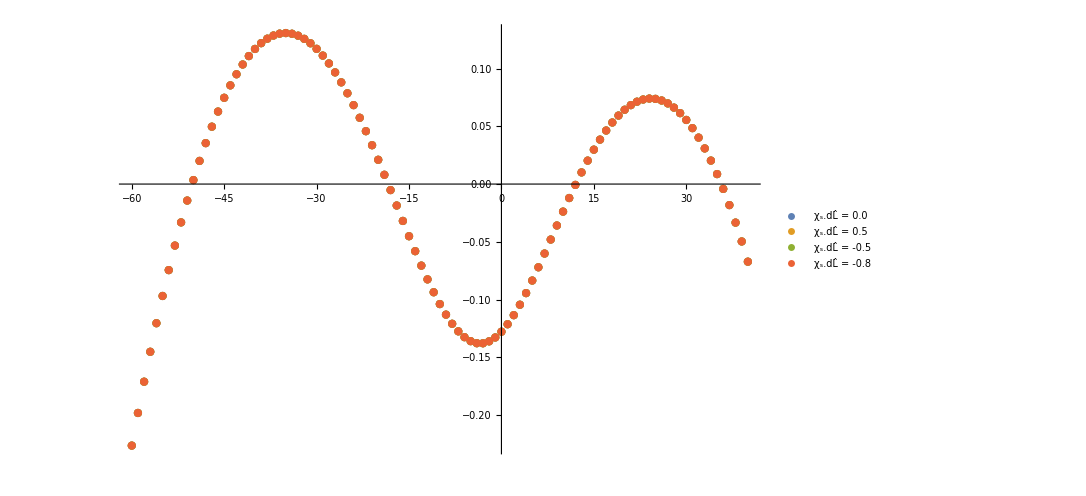

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.0, 0.0, -60, 40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0.5,-0.5, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.5,0.5, -60, 40, 1 ]},Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,0.8, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.0", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```

```mathematica
DataResS0= Transpose@{Range[-60, 40, 1],ResFinal[ 0.0, 0.0, -60, 40,1 ]};
DataResS0p9= Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60, 40,1 ]};
DataResSm0p8= Transpose@{Range[-60, 40, 1],ResFinal[ -0.8, -0.8, -60, 40,1 ]};
```

```mathematica
PolyfitDataResS0 = Fit[DataResS0, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResS0p9 = Fit[DataResS0p9, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResSm0p8 = Fit[DataResSm0p8, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
```

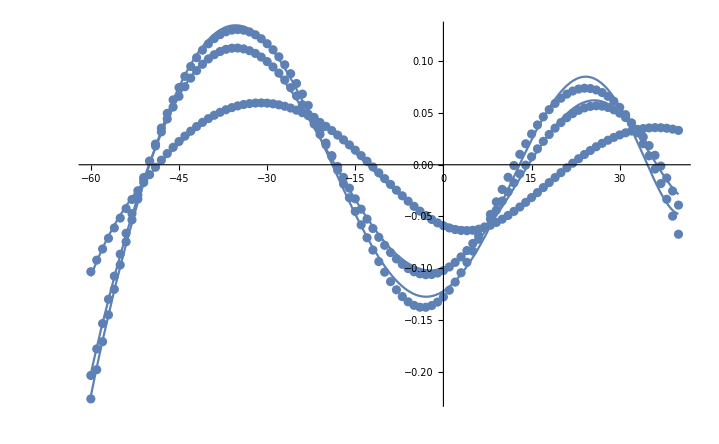

```mathematica
Show[ListPlot[DataResS0], Plot[PolyfitDataResS0, {x, -60 , 40}],ListPlot[DataResS0p9], Plot[PolyfitDataResS0p9, {x, -60 , 40}],ListPlot[DataResSm0p8], Plot[PolyfitDataResSm0p8, {x, -60 , 40}]]
```

```mathematica
(*Define Resedual function using polynomial fit*)
PolyResS0[t_]:= PolyfitDataResS0/.x-> t
PolyResS0p9[t_]:= PolyfitDataResS0p9/.x-> t
PolyResSm0p8[t_]:= PolyfitDataResSm0p8 /.x-> t
```

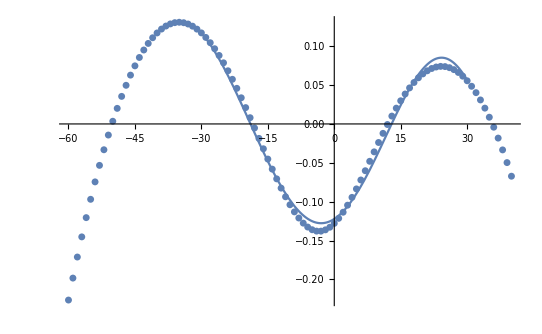

```mathematica
Show[ListPlot[DataResS0], Plot[PolyResS0[t], {t, -30 , 30}]]
```

```mathematica
(*Define function to take nonzero value only insude the observation time*)
ResS0[t_, ti_, tf_]:= Piecewise[{{PolyResS0[t], ti≤ t ≤tf}}, 0]
ResS0p9[t_, ti_, tf_]:= Piecewise[{{PolyResS0p9[t], ti≤ t ≤tf}}, 0]
ResSm0p8[t_, ti_, tf_]:= Piecewise[{{PolyResSm0p8[t], ti≤ t ≤tf}}, 0]
```

```mathematica
(*Taking analytical fourier transform *)
FTS0I1[ω]= Simplify[FourierTransform[ResS0[t, -55, 35], t, ω]Conjugate[FourierTransform[ResS0[t, -55, 35], t, ω]]//ComplexExpand];
FTS0p9I1[ω]= Simplify[FourierTransform[ResS0p9[t, -55, 35], t, ω]Conjugate[FourierTransform[ResS0p9[t, -55, 35], t, ω]]//ComplexExpand];
FTSm0p8I1[ω]= Simplify[FourierTransform[ResSm0p8[t, -55, 35], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -55, 35], t, ω]]//ComplexExpand];
FTS0I2[ω]= Simplify[FourierTransform[ResS0[t, -65, 45], t, ω]Conjugate[FourierTransform[ResS0[t, -65, 45], t, ω]]//ComplexExpand];
FTS0p9I2[ω]= Simplify[FourierTransform[ResS0p9[t, -65, 45], t, ω]Conjugate[FourierTransform[ResS0p9[t, -65, 45], t, ω]]//ComplexExpand];FTSm0p8I2[ω]= Simplify[FourierTransform[ResSm0p8[t, -65, 45], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -65, 45], t, ω]]//ComplexExpand];
```

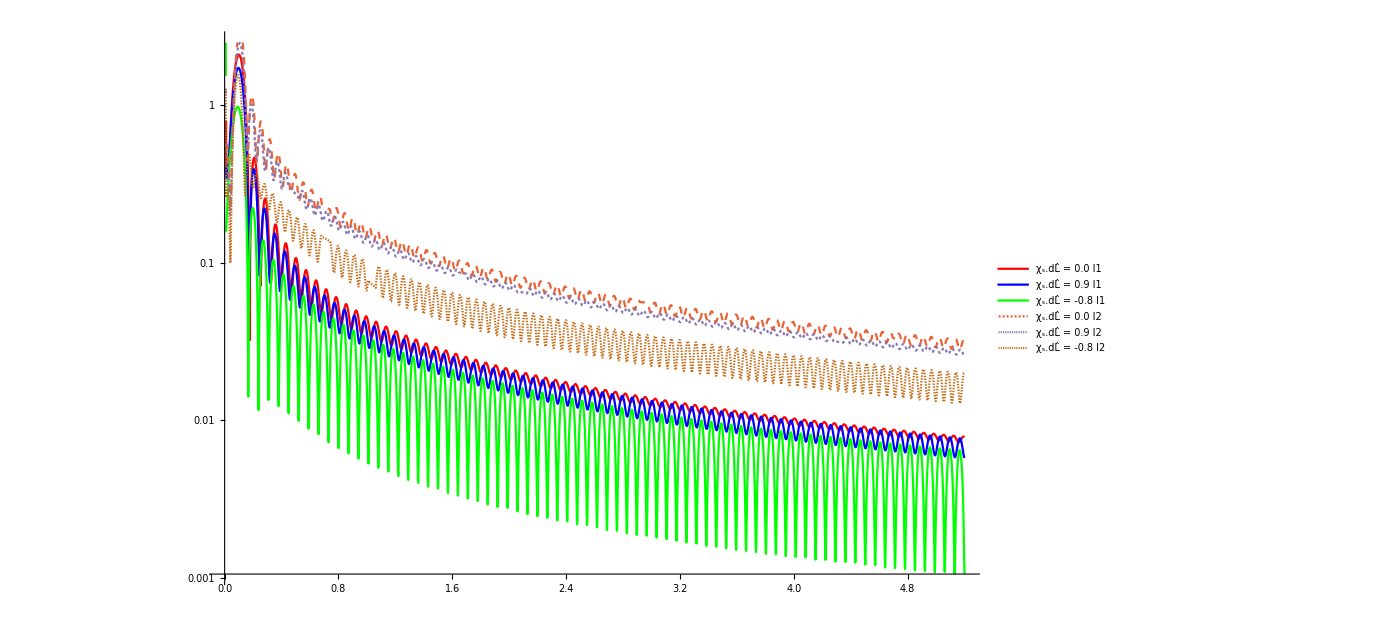

```mathematica
LogPlot[{Sqrt[Abs[FTS0I1[ω]]],Sqrt[Abs[FTS0p9I1[ω]]], Sqrt[Abs[FTSm0p8I1[ω]]] , Sqrt[Abs[FTS0I2[ω]]],Sqrt[Abs[FTS0p9I2[ω]]],Sqrt[ Abs[FTSm0p8I2[ω]]]}, {ω, 0.00001, 5.2}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I1", "χ_s.dL̂ = 0.9 I1","χ_s.dL̂ = -0.8 I1", "χ_s.dL̂ = 0.0 I2", "χ_s.dL̂ = 0.9 I2","χ_s.dL̂ = -0.8 I2"},{0.650,0.7}],PlotStyle-> {Red, Blue,Green,Dashing[0.005],Dashing[0.002], Dashing[0.001]}]
```

```mathematica
FTS0I3[ω]= Simplify[FourierTransform[ResS0[t, -60,40], t, ω]Conjugate[FourierTransform[ResS0[t, -60, 40], t, ω]]//ComplexExpand];
FTS0p9I3[ω]= Simplify[FourierTransform[ResS0p9[t, -60, 40], t, ω]Conjugate[FourierTransform[ResS0p9[t, -60, 40], t, ω]]//ComplexExpand];
FTSm0p8I3[ω]= Simplify[FourierTransform[ResSm0p8[t, -60, 40], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -60, 40], t, ω]]//ComplexExpand];
```

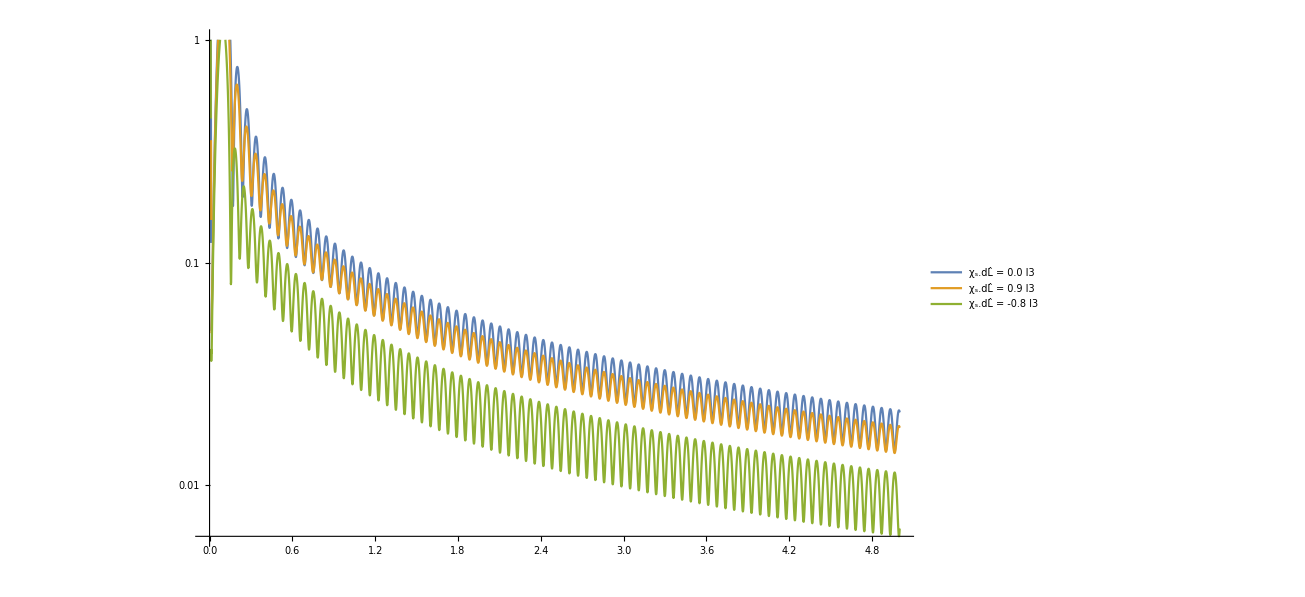

```mathematica
LogPlot[{Sqrt[Abs[FTS0I3[ω]]],Sqrt[Abs[FTS0p9I3[ω]]], Sqrt[Abs[FTSm0p8I3[ω]]]}, {ω,0.00001,5.0}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I3", "χ_s.dL̂ = 0.9 I3","χ_s.dL̂ = -0.8 I3"},{0.150,0.2}]]
```

```mathematica
Sinf[t_]:= Piecewise[{{Sin[t]+ Sin[5t]+ Sin[40t], -8≤ t ≤8}}, 0]
Cosf[t_]:= Piecewise[{{Cos[3t], -8π≤ t ≤8π}}, 0]
SinCosf[t_]:= Piecewise[{{Cos[3t] + Sin[t], -π≤ t ≤π}}, 0]
```

```mathematica
FTSin[ω]= Simplify[FourierTransform[Sinf[t], t, ω]Conjugate[FourierTransform[Sinf[t], t, ω]]//ComplexExpand];
FTCos[ω]= Simplify[FourierTransform[Cosf[t], t, ω]Conjugate[FourierTransform[Cosf[t], t, ω]]//ComplexExpand];
FTSinCos[ω]= Simplify[FourierTransform[SinCosf[t], t, ω]Conjugate[FourierTransform[SinCosf[t], t, ω]]//ComplexExpand];
```

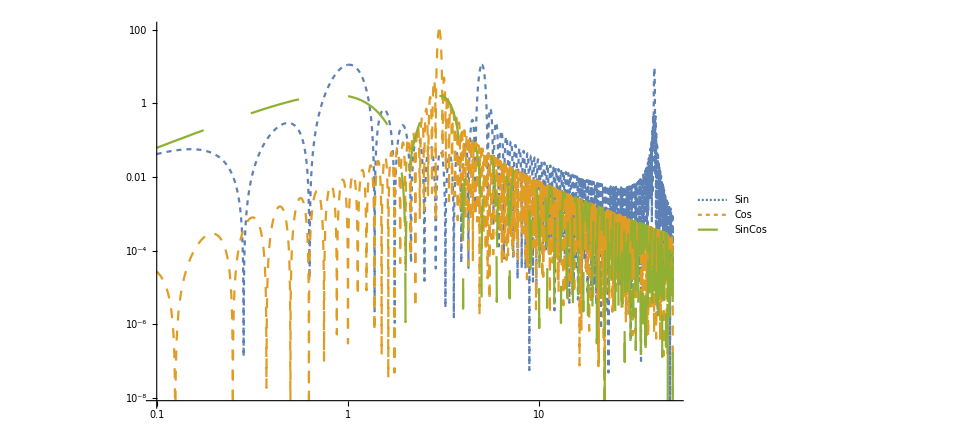

```mathematica
LogLogPlot[{Abs[FTSin[ω]], Abs[FTCos[ω]],Abs[FTSinCos[ω]]}, {ω, 0.1, 50}, PlotStyle-> {Dashing[0.005], Dashing[0.01], Dashing[0.05]}, PlotLegends->Placed[{"Sin", "Cos","SinCos"},{0.150,0.8}]]
```

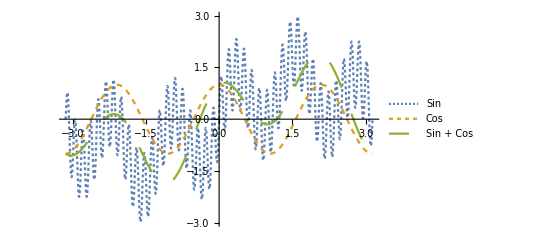

```mathematica
Plot[{Sinf[t], Cosf[t], SinCosf[t]}, {t, -π, π}, PlotStyle-> {Dashing[0.005], Dashing[0.01], Dashing[0.05]}, PlotLegends->Placed[{"Sin", "Cos","Sin + Cos"},{0.150,0.8}]]
```

```mathematica
ResS0period[t_, ti_, tf_]:=  Piecewise[{{PolyResS0[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
ResS0p9period[t_, ti_, tf_]:= Piecewise[{{PolyResS0p9[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
ResSm0p8period[t_, ti_, tf_]:=Piecewise[{{ PolyResSm0p8[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
```

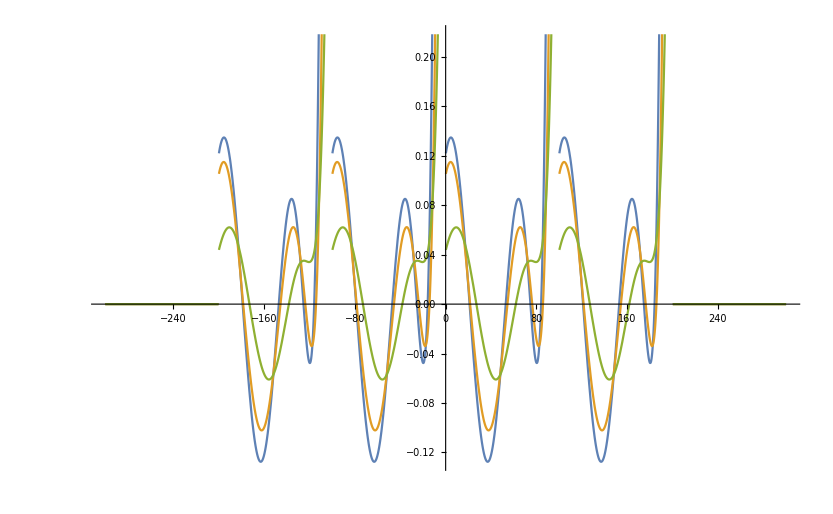

```mathematica
Plot[{ResS0period[t, -60, 40], ResS0p9period[t, -60, 40], ResSm0p8period[t, -60, 40]}, {t, -300, 300}]
```

```mathematica
FTS0period[ω]= Simplify[FourierTransform[ResS0period[t, -60, 40], t, ω]Conjugate[FourierTransform[ResS0period[t, -60, 40], t, ω]]//ComplexExpand];
FTS0p9period[ω]= Simplify[FourierTransform[ResS0p9period[t, -60, 40], t, ω]Conjugate[FourierTransform[ResS0p9period[t, -60, 40], t, ω]]//ComplexExpand];
FTSm0p8period[ω]= Simplify[FourierTransform[ResSm0p8period[t, -60, 40], t, ω]Conjugate[FourierTransform[ResSm0p8period[t, -60, 40], t, ω]]//ComplexExpand];
```

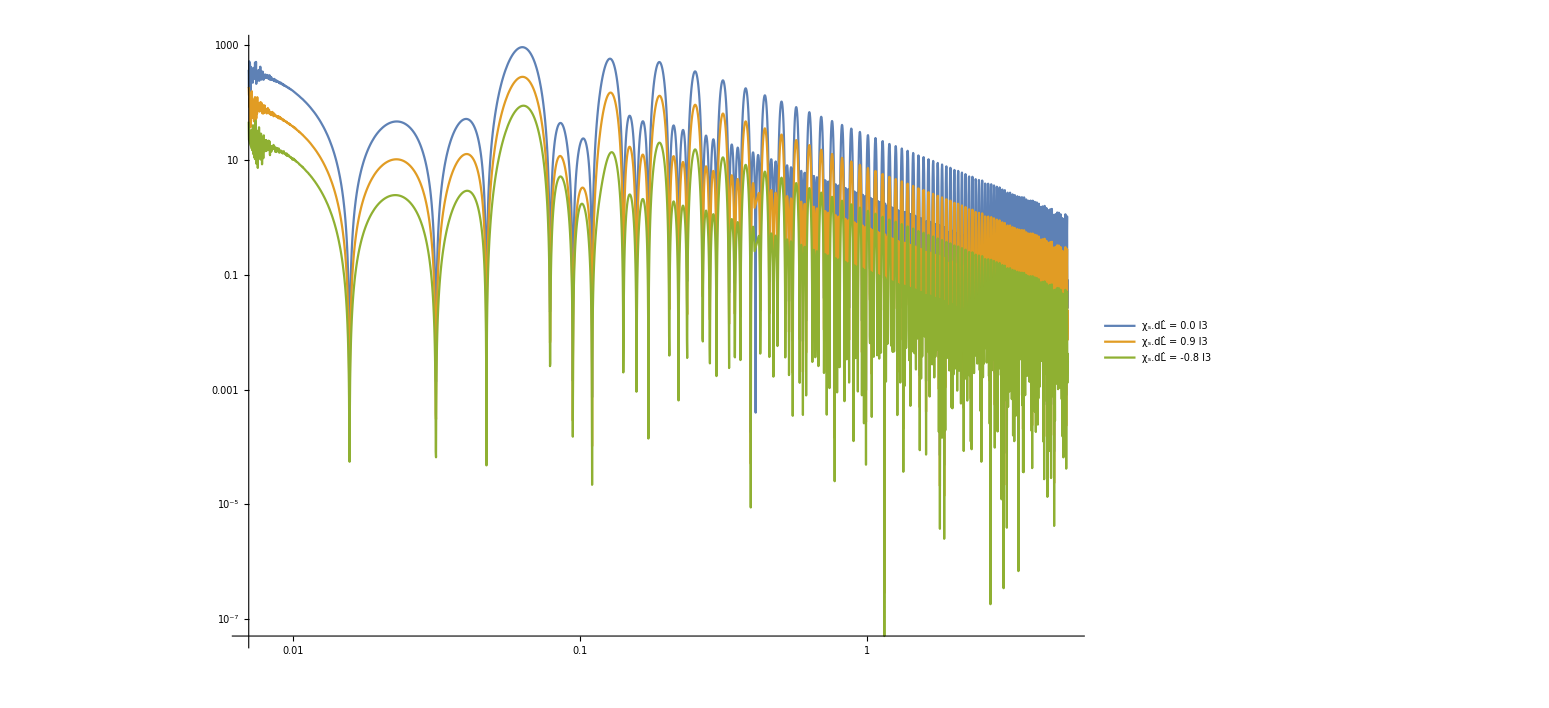

```mathematica
LogLogPlot[{Abs[FTS0period[ω]],Abs[FTS0p9period[ω]], Abs[FTSm0p8period[ω]]}, {ω,0.007,5}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I3", "χ_s.dL̂ = 0.9 I3","χ_s.dL̂ = -0.8 I3"},{0.150,0.2}]]
```

```mathematica
Xt[t_]:= Exp[-Abs[t]]
```

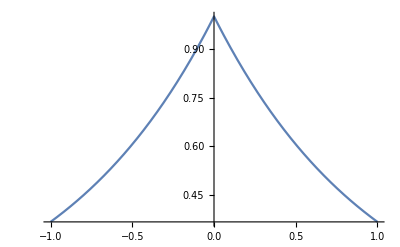

```mathematica
Plot[Xt[t], {t, -1, 1}]
```

```mathematica
FTXt[ω]= Sqrt[Simplify[FourierTransform[Xt[t], t, ω]Conjugate[FourierTransform[Xt[t], t, ω]]//ComplexExpand]]
```

√(2/π) √(1/((1+ω^2)^2))

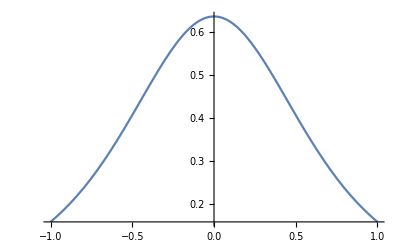

```mathematica
Plot[FTXt[ω], {ω, -1, 1}]
```